```mathematica
(*Dune Experiment
Muon neutrino to Electron Neutrino
inverted hierachy Hierachy*)
```

```mathematica
A11= Cos[θ21]Cos[θ31]
A21= Sin[θ21] Cos[θ31]
A31= Sin[θ31] Exp[-I*σ]
A32= Sin[θ31]Exp[I*σ]
B11=-(Sin[θ21]Cos[θ32])-(Cos[θ21]Sin[θ32]Sin[θ31]Exp[I*σ])
B12= -(Sin[θ21]Cos[θ32])-(Cos[θ21]Sin[θ32]Sin[θ31]Exp[-I*σ])
B21=((Cos[θ21]Cos[θ32])-(Sin[θ21]Sin[θ32]Sin[θ31]Exp[I*σ]))
B22=((Cos[θ21]Cos[θ32])-(Sin[θ21]Sin[θ32]Sin[θ31]Exp[-I*σ]))
B31=Sin[θ32]Cos[θ31]
B32=B31
δm32=δm31-δm21
Abs[δm32]>Abs[δm31]
```

Cos[θ21] Cos[θ31]

Cos[θ31] Sin[θ21]

ⅇ^(-ⅈ σ) Sin[θ31]

ⅇ^(ⅈ σ) Sin[θ31]

-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]

-Cos[θ32] Sin[θ21]-ⅇ^(-ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]

Cos[θ21] Cos[θ32]-ⅇ^(ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32]

Cos[θ21] Cos[θ32]-ⅇ^(-ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32]

Cos[θ31] Sin[θ32]

Cos[θ31] Sin[θ32]

-δm21+δm31

Abs[-δm21+δm31]>Abs[δm31]

```mathematica
P1=0
P2=4Re[((B22*A21*B11*A11)*(Sin[(((δm21))*(l/e)*1.27)])^2)+((B32*A31*B21*A21)*(Sin[(((δm32))*(l/e)*1.27 )])^2)+((B32*A31*B11*A11)*(Sin[(((δm31))*(l/e)*1.27)])^2)]
P3=2Im[(((B22*A21*B11*A11)Sin[(((((δm21))*(l/(2e))*1.27*4)))])+((B32*A31*B21*A21)Sin[((((δm32))*(l/(2e))*1.27*4))])+((B32*A31*B11*A11)Sin[((((δm31))*(l/(2e))*1.27*4))]))]
```

0

4 Re[ⅇ^(-ⅈ σ) Cos[θ21] Cos[θ31]^2 Sin[(1.27 l δm31)/e]^2 Sin[θ31] Sin[θ32] (-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32])+Cos[θ21] Cos[θ31]^2 Sin[(1.27 l δm21)/e]^2 Sin[θ21] (-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]) (Cos[θ21] Cos[θ32]-ⅇ^(-ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])+ⅇ^(-ⅈ σ) Cos[θ31]^2 Sin[(1.27 l (-δm21+δm31))/e]^2 Sin[θ21] Sin[θ31] Sin[θ32] (Cos[θ21] Cos[θ32]-ⅇ^(ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])]

2 Im[ⅇ^(-ⅈ σ) Cos[θ21] Cos[θ31]^2 Sin[(2.54 l δm31)/e] Sin[θ31] Sin[θ32] (-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32])+Cos[θ21] Cos[θ31]^2 Sin[(2.54 l δm21)/e] Sin[θ21] (-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]) (Cos[θ21] Cos[θ32]-ⅇ^(-ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])+ⅇ^(-ⅈ σ) Cos[θ31]^2 Sin[(2.54 l (-δm21+δm31))/e] Sin[θ21] Sin[θ31] Sin[θ32] (Cos[θ21] Cos[θ32]-ⅇ^(ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])]

```mathematica
i[e_,σ_]=P1-P2+P3 /.{θ21->0.6021386,
θ31->0.1467822,
θ32->0.8813913,
δm21->7.56*^-5,
δm31->-2.49*^-3,l->1300}
```

2 Im[0.456805 (0.524209-0.0639215 ⅇ^(-ⅈ σ)) (-0.360279-0.0930063 ⅇ^(ⅈ σ)) Sin[0.249631/e]-0.0910169 ⅇ^(-ⅈ σ) (-0.360279-0.0930063 ⅇ^(ⅈ σ)) Sin[8.22198/e]-0.0625542 ⅇ^(-ⅈ σ) (0.524209-0.0639215 ⅇ^(ⅈ σ)) Sin[8.47161/e]]-4 Re[0.456805 (0.524209-0.0639215 ⅇ^(-ⅈ σ)) (-0.360279-0.0930063 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0910169 ⅇ^(-ⅈ σ) (-0.360279-0.0930063 ⅇ^(ⅈ σ)) Sin[4.11099/e]^2+0.0625542 ⅇ^(-ⅈ σ) (0.524209-0.0639215 ⅇ^(ⅈ σ)) Sin[4.23581/e]^2]

```mathematica
(*f[e_,σ_]=P1-P2+P3 /.{θ21->0.594371,
θ31->0.160875,
θ32->0.698357,
δm21->Sqrt[8*^-5],
δm32->-Sqrt[2.3*^-3],
l->1300}*)
```

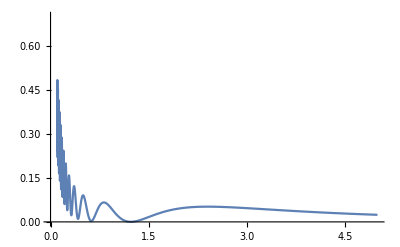

```mathematica
g1=Plot[i[e,0],{e,0.1,5},PlotRange->{0,0.7}]
```

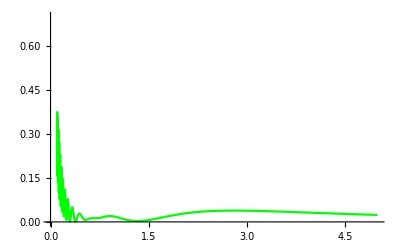

```mathematica
g2=Plot[i[e,π/2],{e,0.1,5},PlotRange->{0,0.7},PlotStyle->Green]
```

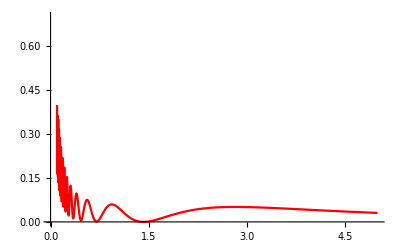

```mathematica
g3=Plot[i[e,π],{e,0.1,5},PlotRange->{0,0.7},PlotStyle->Red]
```

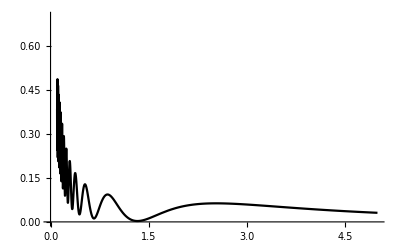

```mathematica
g4=Plot[i[e,3π/2],{e,0.1,5},PlotRange->{0,0.7},PlotStyle->Black]
```

```mathematica
7
```

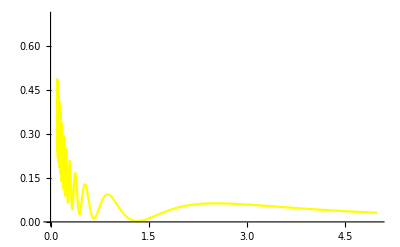

```mathematica
g5=Plot[i[e,-π/2],{e,0.1,5},PlotRange->{0,0.7},PlotStyle->Yellow]
```

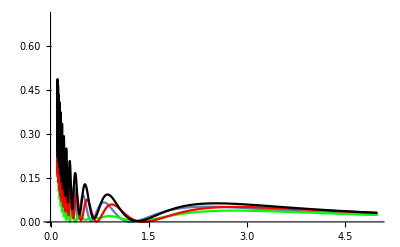

```mathematica
Show[g1,g2,g3,g4]
```

```mathematica
Manipulate[Plot[f[e,σ],{e,0.1,5},PlotRange->{0,1}],{σ,0,2π}]
```

```mathematica
Manipulate[Plot[(f[e,σ]-f[e,-σ])/(f[e,σ]+f[e,-σ]),{e,0.1,5},PlotRange->{-1,1}],{σ,0,2π}]
```

```mathematica
1300/550
```

26/11

```mathematica
N[26/11]
```

2.36364